## Homogenous vs Non-Homogenous ODEs Laplace/Traditional Solution Approach

x^(..)(t) + 4x(t) =0
with x(0) = 5
           ẋ(0) = -3

We can first find the homogeneous solution.We can look at the characteristic equation.

   r^2+ 4 = 0
Solving for the roots of the char equation yields

```mathematica
ClearAll["Global`*"]
theroots = Solve[r^2+4 ==0,r]
```

{{r→-2 ⅈ},{r→2 ⅈ}}

So the roots are r1 = -2i, r2 = 2i .These are distinct  roots but not real.Let us assume for the distinct-real roots case

x_homogenous =c_1 e^r1t+ c_2 e^r2t

```mathematica
xhomogeneous[t_]=c1 Exp[r1 t]+c2 Exp[r2 t]/.{r1->-2 I,r2->2 I}
```

c1 ⅇ^(-2 ⅈ t)+c2 ⅇ^(2 ⅈ t)

We note that this solves differential equation

```mathematica
D[xhomogeneous[t],{t,2}]+ 4 xhomogeneous[t]==0// Simplify
```

True

We can now apply initial conditions to solve for c1 and c2

```mathematica
xDothomogeneous[t_]= D[xhomogeneous[t],t];
temp = 
Solve[{xhomogeneous[0]==5,xDothomogeneous[0]==-3},{c1,c2}]
c1 = c1/. temp[[1]]
c2 = c2 /. temp[[1]]
```

{{c1→5/2-(3 ⅈ)/4,c2→5/2+(3 ⅈ)/4}}

5/2-(3 ⅈ)/4

5/2+(3 ⅈ)/4

so the proposed solution is

```mathematica
xhomogeneous[t]
```

(5/2-(3 ⅈ)/4) ⅇ^(-2 ⅈ t)+(5/2+(3 ⅈ)/4) ⅇ^(2 ⅈ t)

Let' s check that  the initial conditions

```mathematica
xhomogeneous[0]
xDothomogeneous[0]
```

5

-3

writing form of Euler’s Formula = e^iθ= cosθ+sinθi

```mathematica
solution [t_]= ExpToTrig[xhomogeneous[t]]
```

5 Cos[2 t]-3/2 Sin[2 t]

Imaginary roots lead to escillatory solutions.Hence,another form of solution to assume this
x_homogenous(t) = e^σt(c1cos(ωt) + c2sin(ωt))

where    r = σ + ωi and our roots don’t have real number so 
σ = 0

```mathematica
Clear[c1,c2]
```

```mathematica
xhomogeneous[t_]=c1 Cos[2 t]+ c2 Sin[2 t]
```

c1 Cos[2 t]+c2 Sin[2 t]

Lets verify this  also satisfies the differential equation

```mathematica
D[xhomogeneous[t],{t,2}]+ 4 xhomogeneous[t]==0 // Simplify
```

True

```mathematica
(* We can now apply the ICs*)
```

```mathematica
xDothomogeneous[t_]=D[xhomogeneous[t],t]; 
temp = Solve[{xhomogeneous[0]==5,xDothomogeneous[0]== -3},{c1,c2}];
c1 = c1/.temp[[1]]
c2 = c2/. temp[[1]]
```

5

-3/2

```mathematica
xhomogeneous[t]
```

5 Cos[2 t]-3/2 Sin[2 t]

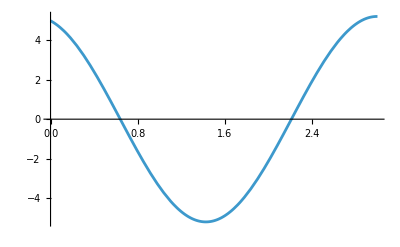

```mathematica
Plot[xhomogeneous[t],{t,0,3}]
```

```mathematica
xhomogeneous[t]==solution[t]
```

True

## Non-Homogeneous ODE

x^(..)(t) + 4x(t) =2 sin(3t)
with x(0) = 5
           ẋ(0) = -3

```mathematica
g[t_]= 2 Sin[3 t]
```

2 Sin[3 t]

2 Sin[3 t]
We already know our homogenous response,characterisc equation that

```mathematica
r1 = r/.theroots[[1]]
r2 = r/.theroots[[2]]
```

-2 ⅈ

2 ⅈ

```mathematica
2 ⅈ
xhomogenous2[t_]= c3 Exp[r1 t]+ c4 Exp[r2 t]
```

2 ⅈ

c3 ⅇ^(-2 ⅈ t)+c4 ⅇ^(2 ⅈ t)

For traditional Approach

```mathematica
xparticular[t_]= A Sin[3 t]
```

A Sin[3 t]

```mathematica
D[xparticular[t],{t,2}]+ 4 xparticular[t]// FullSimplify
```

-5 A Sin[3 t]

```mathematica
-5 A Sin[3 t]
```

-5 A Sin[3 t]

-5Asin(3t) = 2 Sin(3t)

Hence A = -2/5, so  the particular solution is 
x(t) = ϕ(t) = c_1 x_homogeneous(t) +  c_2 x_homogeneous(t) +x_particular(t)

```mathematica
A = -2/5;
```

```mathematica
x[t_] = xhomogenous2[t]+ xparticular[t]
```

c3 ⅇ^(-2 ⅈ t)+c4 ⅇ^(2 ⅈ t)-2/5 Sin[3 t]

```mathematica
D[x[t],{t,2}]+ 4 x[t]==g[t] // FullSimplify
```

True

```mathematica
dx[t_]= D[x[t],t];
temp2 = Solve[{x[0]==5,dx[0]==-3},{c3,c4}];
c3= c3/.temp2[[1]]
c4 = c4/.temp2[[1]]
```

5/2-(9 ⅈ)/20

5/2+(9 ⅈ)/20

```mathematica
x[0]==5
```

True

```mathematica
True
(D[x[t],t]/.{t->0}) ==-3
```

True

True

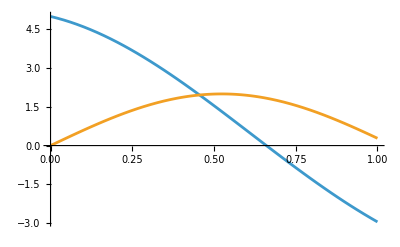

```mathematica
P1 = Plot[{x[t],g[t]},{t,0,1},
PlotRange->All]
```

### Compare with the Laplace Tecnique

Recalling the original ODE 
              x^(..)(t) + 4x(t) =2 sin(3t)
              L[x^(..)(t) + 4x(t) ] = 2L[sin(3t)]
              (s^2X(s)-sx(0)-ẋ(0))+4X(s) =(2*3)/(s^2+3^2)     note x(0)=5,ẋ(0)  =-3

```mathematica
Solve[(s^2 X-5 s+3)+ 4 X==6/(s^2+9),X]
```

{{X→(-21+45 s-3 s^2+5 s^3)/((4+s^2) (9+s^2))}}

```mathematica
Solve[(4+s^2) (9+s^2)==0,s]
```

{{s→-2 ⅈ},{s→2 ⅈ},{s→-3 ⅈ},{s→3 ⅈ}}

So the roots are not real,they are complex conjugate.We do PFE:

```mathematica
F[s_]= (2+5 s)/(s^2+4)+(1+4 s)/(s^2+9)
```

(2+5 s)/(4+s^2)+(1+4 s)/(9+s^2)

```mathematica
F[t_]=InverseLaplaceTransform[F[s],s,t]
```

5 Cos[2 t]+4 Cos[3 t]+Sin[2 t]+1/3 Sin[3 t]

and Voila! Our physical response  f(t)= 5 Cos[2 t]+4 Cos[3 t]+Sin[2 t]+1/3 Sin[3 t]

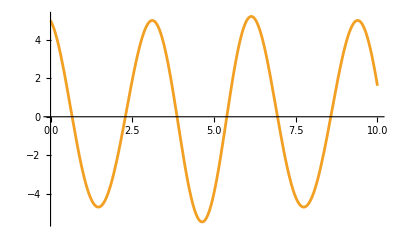

```mathematica
Plot[{F[t],x[t]},{t,0,10}]
```

As it shown above, we can verify that , the both tecniques are the same.

Set::write: Tag LaplaceTransform in LaplaceTransform[LaplaceTransform[LaplaceTransform[(4\ x[t] + SuperscriptBox["x", "′",MultilineFunction->None][t])[t], t, s][t], t, s][t], t, s] is Protected.

Set::write: Tag Times in (2 Sin[3 t])[t_] is Protected.